## Data Import

```mathematica
Function Definitions
```

Definitions Function

```mathematica
(* format data into what mathematica likes - horribly inefficient, but oh well *) 
datamould[datain_]:= Module[{data,testdata,wavelengths,times,final}, 
(* take the times *) 
times=datain[[1,2;;]];
data = datain[[2;;]];

(* transpose *) 
data=Transpose[data];
(* remove zeros *) 
data = DeleteCases[data[[#]],0.,Infinity]&/@ Range[Length[data]];

(* take the wavelengths *) 
wavelengths = data[[1]];
data=data[[2;;]];

testdata = data;

(* For each of time data, add on times *) 
For[i=1,i≤ Length[times], i++, 
testdata[[i]]=Append[{times[[i]]},data[[i,#]]]&/@ Range[Length[data[[i]]]];
] ;

final =ConstantArray[0,Length[wavelengths]-10];

(* For each of wavelength data, add on wavelength *)
For[i=1,i≤ Length[wavelengths]-10, i++, 
final[[i]]=Flatten[Append[{wavelengths[[i]]},testdata[[#,i]]]]&/@ Range[Length[data]];
] ;

final = Flatten[final,1];

For[i=1, i≤ Length[final], i++, 
final[[i]] = {final[[i,2]],final[[i,1]],final[[i,3]]};
];
Return[final];
]
```

```mathematica
Analysis
```

Analysis

```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames["./wtfs/*wtf"]
importfiles= Import[#,"Data"]&/@files;
```

{./wtfs/420nm_Sphingo_0p6mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_6803_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_7120_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_7942_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_Arabidopsis_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_Chlamy_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_Phaeo_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_sfGFPVnat_0p7mW_3_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/460nm_Smicro_0p7mW_3_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/500nm_mScarlet_0p55mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/500nm_Rhodo_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf}

```mathematica
shingow420=datamould[importfiles[[1]]];
sync6803w460=datamould[importfiles[[2]]];
sync7120w460=datamould[importfiles[[3]]];
sync7942w460=datamould[importfiles[[4]]];
arabidopsisw460=datamould[importfiles[[5]]];
chlamyw460=datamould[importfiles[[6]]];
phaeow460=datamould[importfiles[[7]]];
sfGFPVnatw460=datamould[importfiles[[8]]];
smicrow460=datamould[importfiles[[9]]];
mScarlet500=datamould[importfiles[[10]]];
rhodo500=datamould[importfiles[[11]]];
```

```mathematica
(* --------------- *) 

SetDirectory[NotebookDirectory[]];
files=FileNames["./wtfs/singleshots/*wtf"]
importfiles= Import[#,"Data"]&/@files;

phaeow460single=datamould[importfiles[[1]]];
mScarlet500single=datamould[importfiles[[2]]];
```

{./wtfs/singleshots/460nm_Phaeo_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/singleshots/500nm_mScarlet_0p55mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./wtfs/singleshots/meas_1.wtf}

```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames["./microwtfs/*wtf"]
microwtfs= Import[#,"Data"]&/@files;
smicrow4602=datamould[microwtfs[[2]]];
smicrow4603=datamould[microwtfs[[3]]];
```

{./microwtfs/460nm_Smicro_0p7mW_2_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./microwtfs/460nm_Smicro_0p7mW_3_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf,./microwtfs/460nm_Smicro_0p7mW_495nm_12uW_NA_POL_Pump_NA_POL_Probe.wtf}

```mathematica
datain=microwtfs[[1]];
times=datain[[1,2;;]];
data = datain[[2;;]];

(* transpose *) 
data=Transpose[data];
(* remove zeros *) 
data = DeleteCases[data[[#]],0.,Infinity]&/@ Range[Length[data]];

(* take the wavelengths *) 
wavelengths = data[[1]];
data=data[[2;;]];

testdata = data;

(* For each of time data, add on times *) 
For[i=1,i≤ Length[times], i++, 
testdata[[i]]=Append[{times[[i]]},data[[i,#]]]&/@ Range[Length[data[[i]]]];
] ;

final =ConstantArray[0,Length[wavelengths]-10];

(* For each of wavelength data, add on wavelength *)
For[i=1,i≤ Length[wavelengths]-10-5, i++, 
final[[i]]=Flatten[Append[{wavelengths[[i]]},testdata[[#,i]]]]&/@ Range[Length[data]-7];
] ;

final = Flatten[final,1];

For[i=1, i≤ Length[final]-7, i++, 
final[[i]] = {final[[i,2]],final[[i,1]],final[[i,3]]};
];

smicrow4601=final[[;;-7]];
```

## Interpolation and Initial Analysis

```mathematica
Function Definitions
```

Definitions Function

```mathematica
converttoOD[data_]:=Module[{x,y,selection,datahold}, 
datahold=data; 
datahold = -Log[10,datahold+1];
Return[datahold];
]
```

```mathematica
Analysis
```

Analysis

```mathematica
(* Convert DT/T data to OD *) 
shingow420[[;;,3]] = converttoOD[shingow420[[;;,3]]] ;
sync6803w460[[;;,3]] = converttoOD[sync6803w460[[;;,3]]] ;
sync7120w460[[;;,3]] = converttoOD[sync7120w460[[;;,3]]] ;
sync7942w460[[;;,3]] = converttoOD[sync7942w460[[;;,3]]] ;
arabidopsisw460[[;;,3]] = converttoOD[arabidopsisw460[[;;,3]]] ;
chlamyw460[[;;,3]] = converttoOD[chlamyw460[[;;,3]]] ;
phaeow460[[;;,3]] = converttoOD[phaeow460[[;;,3]]] ;
sfGFPVnatw460[[;;,3]] = converttoOD[sfGFPVnatw460[[;;,3]]] ;
smicrow460[[;;,3]] = converttoOD[smicrow460[[;;,3]]] ;
mScarlet500[[;;,3]] = converttoOD[mScarlet500[[;;,3]]] ;
rhodo500[[;;,3]] = converttoOD[rhodo500[[;;,3]]] ;
```

```mathematica
phaeow460single[[;;,3]] = converttoOD[phaeow460single[[;;,3]]];
mScarlet500single[[;;,3]]= converttoOD[mScarlet500single[[;;,3]]];
```

```mathematica
smicrow4601[[;;,3]]=converttoOD[smicrow4601[[;;,3]]];
smicrow4602[[;;,3]]=converttoOD[smicrow4602[[;;,3]]];
smicrow4603[[;;,3]]=converttoOD[smicrow4603[[;;,3]]];
```

```mathematica
(* Interpolations from real data *) 
(* Form: time_, wavelength_ *) 
shingow420int = Interpolation[shingow420,InterpolationOrder->1];
sync6803w460int = Interpolation[sync6803w460,InterpolationOrder->1];
sync7120w460int = Interpolation[sync7120w460,InterpolationOrder->1];
sync7942w460int = Interpolation[sync7942w460,InterpolationOrder->1];
arabidopsisw460int = Interpolation[arabidopsisw460,InterpolationOrder->1];
chlamyw460int = Interpolation[chlamyw460,InterpolationOrder->1];
phaeow460int = Interpolation[phaeow460,InterpolationOrder->1];
sfGFPVnatw460int = Interpolation[sfGFPVnatw460,InterpolationOrder->1];
smicrow460int = Interpolation[smicrow460,InterpolationOrder->1];
mScarlet500int = Interpolation[mScarlet500,InterpolationOrder->1];
rhodo500int = Interpolation[rhodo500,InterpolationOrder->1];
```

```mathematica
phaeow460singleint = Interpolation[phaeow460single,InterpolationOrder->1];
mScarlet500singleint = Interpolation[mScarlet500single,InterpolationOrder->1];
```

```mathematica
smicrow4601int = Interpolation[smicrow4601,InterpolationOrder->1];
smicrow4602int = Interpolation[smicrow4602,InterpolationOrder->1];
smicrow4603int = Interpolation[smicrow4603,InterpolationOrder->1];
```

-Graphics-

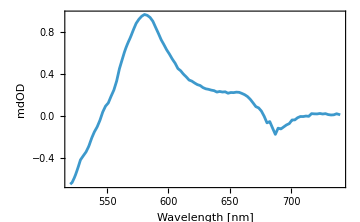

{145,245,3}

```mathematica
(* -------------------- sync7942w460int ------------------------ *)

sync7942w460int2[t_,w_]:=Module[{},result = sync7942w460int[t,w]-Mean[sync7942w460int[#,w]&/@Table[i,{i,0,-2000,-50}]]];

plot2=DensityPlot[1000*sync7942w460int2[t*1000,w],{w,520,740},{t,-2,50},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

Plot[{1000*Mean[Table[sync7942w460int2[t,w],{t,100,1000,200}]]},{w,520,740},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[sync7942w460[[;;,1]]];
wavs=DeleteDuplicates[sync7942w460[[;;,2]]];
map=Table[{t,nm,sync7942w460int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./sync7942w460_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
```

-Graphics-

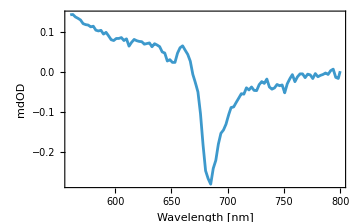

{145,245,3}

./arabidopsisw460_wavelengths.csv

```mathematica
(* -------------------- arabidopsisw460int ------------------------ *)


arabidopsisw460int2[t_,w_]:=Module[{},result = arabidopsisw460int[t,w]-Mean[arabidopsisw460int[#,w]&/@Table[i,{i,0,-2000,-50}]]];

plot2=DensityPlot[1000*arabidopsisw460int2[t*1000,w],{w,560,800},{t,-2,50},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
Plot[{1000*Mean[Table[arabidopsisw460int2[t,w],{t,100,1000,200}]]},{w,560,800},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[arabidopsisw460[[;;,1]]];
wavs=DeleteDuplicates[arabidopsisw460[[;;,2]]];
map=Table[{t,nm,arabidopsisw460int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./arabidopsisw460_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./arabidopsisw460_wavelengths.csv",Table[{w,1000*Mean[Table[arabidopsisw460int2[t,w],{t,100,1000,200}]]},{w,wavs}]]
```

-Graphics-

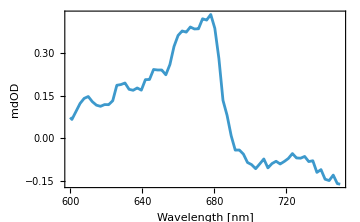

{145,245,3}

./chlamyw460_wavelengths.csv

```mathematica
(* -------------------- chlamyw460int ------------------------ *)


chlamyw460int2[t_,w_]:=Module[{},result = chlamyw460int[t,w]-Mean[chlamyw460int[#,w]&/@Table[i,{i,-100,-2000,-50}]]];

plot2=DensityPlot[1000*chlamyw460int2[t*1000,w],{w,600,750},{t,-2,50},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
Plot[{1000*Mean[Table[chlamyw460int2[t,w],{t,100,20000,200}]]},{w,600,750},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[chlamyw460[[;;,1]]];
wavs=DeleteDuplicates[chlamyw460[[;;,2]]];
map=Table[{t,nm,chlamyw460int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./chlamyw460_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./chlamyw460_wavelengths.csv",Table[{w,1000*Mean[Table[chlamyw460int2[t,w],{t,100,1000,200}]]},{w,wavs}]]
```

-Graphics-

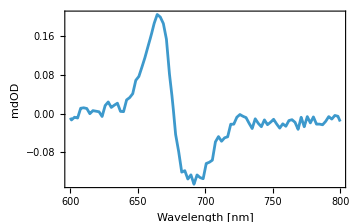

{145,245,3}

./phaeow460_wavelengths.csv

```mathematica
(* -------------------- phaeow460int ------------------------ *)

phaeow460singleint2[t_,w_]:=Module[{},result = phaeow460int[t,w]-Mean[phaeow460int[#,w]&/@Table[i,{i,100,-2000,-100}]]];
plot2=DensityPlot[1000*phaeow460singleint2[t*1000,w],{w,600,750},{t,-2,50},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
Plot[{1000*Mean[Table[phaeow460singleint2[t,w],{t,500,2000,100}]]},{w,600,800},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[phaeow460[[;;,1]]];
wavs=DeleteDuplicates[phaeow460[[;;,2]]];
map=Table[{t,nm,phaeow460singleint2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./phaeow460_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./phaeow460_wavelengths.csv",Table[{w,1000*Mean[Table[phaeow460singleint2[t,w],{t,100,1000,200}]]},{w,wavs}]]
```

```mathematica
interpolation = smicrow460int;
dataset = smicrow460;
smicrow460int2[t_,w_]:=Module[{},result = interpolation[t,w]-Mean[interpolation[#,w]&/@Table[i,{i,100,-1000,-100}]]];
plot2=DensityPlot[1000*smicrow460int2[t*1000,w],{w,550,980},{t,-2,20},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[dataset[[;;,1]]];
wavs=DeleteDuplicates[dataset[[;;,2]]];
map=Table[{t,nm,smicrow460int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./smicrow460_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./smicrow460_wavelengths.csv",Table[{w,1000*Mean[Table[smicrow460int2[t,w],{t,tims[[19+4;;19+20]]}]]},{w,wavs}]]
Export["./smicrow460_wavelengths_2.csv",Table[{w,1000*Mean[Table[smicrow460int2[t,w],{t,tims[[19+20+4;;19+58]]}]]},{w,wavs}]]
Export["./smicrow460_wavelengths_3.csv",Table[{w,1000*Mean[Table[smicrow460int2[t,w],{t,tims[[19+58+4;;19+100]]}]]},{w,wavs}]]
```

-Graphics-

{150,245,3}

./smicrow460_wavelengths.csv

./smicrow460_wavelengths_2.csv

./smicrow460_wavelengths_3.csv

```mathematica
tims[[19+58+4;;19+100]]
```

{13563.1,14563.1,15637.7,16792.5,18033.4,19366.9,20799.9,22339.9,23994.7,25773.,27683.9,29737.4,31944.2,34315.5,36863.8,39602.3,42545.,45707.3,49105.5,52757.2,56681.4,60898.4,65430.,70299.6,75532.6,81156.,87199.,93692.8,100671.,108170.,116228.,124888.,134194.,144194.,154940.,166488.,178897.,192232.,206562.}

InterpolatingFunction::femdmval: Input value {1.25377×10^6,760.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.25377×10^6,761.} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {1.25377×10^6,762.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.98695×10^6,760} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.98695×10^6,761} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.98695×10^6,762} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

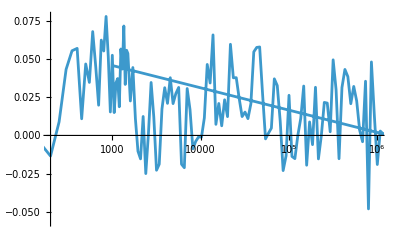

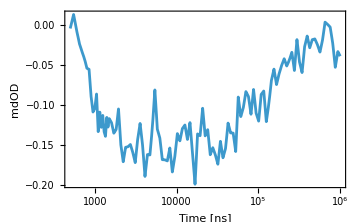

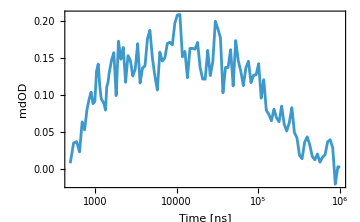

./smicrow_kinetic1.csv

./smicrow_kinetic2.csv

./smicrow_kinetic3.csv

```mathematica
start=775;
stop = 795;
Monitor[avdata=Table[{t,1000*Mean[Table[smicrow460int21[t,w],{w,start,stop}]],1000*Mean[Table[smicrow460int22[t,w],{w,start,stop}]],1000*Mean[Table[smicrow460int23[t,w],{w,start,stop}]]},{t,tims}];,t]
avdata2=avdata;
avdata2=Transpose[{avdata2[[;;,1]],Mean[#]&/@avdata[[;;,2;;4]]}];
ListLogLinearPlot[avdata2,Joined->True,PlotRange->{{200,1000000},{Min[avdata2[[;;,2]]],Max[avdata2[[;;,2]]]}}]

LogLinearPlot[{1000*Mean[Table[smicrow460int2[t,w],{w,640,670}]]},{t,500,1000000},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Time [ns]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
LogLinearPlot[{1000*Mean[Table[smicrow460int2[t,w],{w,680,710}]]},{t,500,1000000},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Time [ns]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

Export["./smicrow_kinetic1.csv",Table[{t,1000*Mean[Table[smicrow460int2[t,w],{w,640,670}]]},{t,tims}]]
Export["./smicrow_kinetic2.csv",Table[{t,1000*Mean[Table[smicrow460int2[t,w],{w,680,710}]]},{t,tims}]]
Export["./smicrow_kinetic3.csv",avdata2]
```

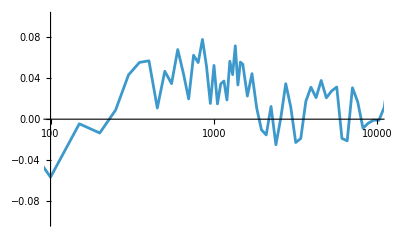

```mathematica
ListLogLinearPlot[avdata2[[;;-2]],Joined->True,PlotRange->{{100,10000},{-1/10,1/10}}]
```

```mathematica
(* -------------------- smicrow460int ------------------------ *)

interpolation1 = smicrow4601int;
dataset = smicrow4601;
smicrow460int21[t_,w_]:=Module[{},result = interpolation1[t,w]-Mean[interpolation1[#,w]&/@Table[i,{i,100,-1000,-100}]]];
tims=DeleteDuplicates[dataset[[;;,1]]];
wavs=DeleteDuplicates[dataset[[;;,2]]];
map=Table[{t,nm,smicrow460int21[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./smicrow460_map_replicate_1.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]]
```

InterpolatingFunction::femdmval: Input value {-2000.,1.07539×10^6} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {100.,1.07539×10^6} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.07539×10^6} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

{139,241,3}

./smicrow460_map_replicate_1.csv

```mathematica
tims
```

{-2000.,-1800.,-1600.,-1400.,-1200.,-1000.,-800.,-600.,-500.,-450.,-400.,-350.,-300.,-250.,-200.,-150.,-100.,-50.,0.,50.,100.,150.,200.,250.,300.,350.,400.,450.,500.,550.,600.,650.,700.,750.,800.,850.,900.,950.,1000.,1050.,1100.,1150.,1200.,1250.,1300.,1350.,1400.,1450.,1500.,1600.,1707.98,1824.57,1950.46,2086.4,2233.18,2391.67,2562.8,2747.58,2947.11,3162.55,3395.18,3646.37,3917.6,4210.46,4526.69,4868.15,5236.84,5634.95,6064.82,6528.97,7030.16,7571.33,8155.67,8786.63,9467.92,10203.6,10997.9,11855.6,12781.7,13781.7,14861.5,16027.4,17286.3,18645.7,20113.5,21698.4,23409.7,25257.5,27252.8,29407.2,31733.6,34245.4,36957.7,39886.4,43048.6,46463.2,50150.1,54131.2,58429.9,63071.4,68083.3,73495.,79338.4,85648.,92460.9,99817.3,107761.,116338.,125599.,135599.,146397.,158056.,170645.,184238.,198916.,214765.,231879.,250357.,270310.,291854.,315117.,340236.,367359.,396645.,428268.,462414.,499283.,539094.,582080.,628496.,678615.,732732.,791166.,854262.,922391.,995955.,1.07539×10^6,1.16116×10^6,1.25377×10^6,1.35377×10^6,1.46175×10^6,1.57834×10^6,1.70423×10^6,1.84017×10^6,1.98695×10^6}

```mathematica
wavs
```

{448.959,451.227,453.496,455.765,458.033,460.302,462.57,464.839,467.107,469.376,471.644,473.913,476.181,478.45,480.718,482.987,485.255,487.524,489.792,492.061,494.329,496.598,498.866,501.135,503.403,505.672,507.94,510.209,512.477,514.746,517.014,519.283,521.551,523.82,526.088,528.357,530.625,532.894,535.162,537.431,539.7,541.968,544.237,546.505,548.774,551.042,553.311,555.579,557.848,560.116,562.385,564.653,566.922,569.19,571.459,573.727,575.996,578.264,580.533,582.801,585.07,587.338,589.607,591.875,594.144,596.412,598.681,600.949,603.218,605.486,607.755,610.023,612.292,614.56,616.829,619.097,621.366,623.635,625.903,628.172,630.44,632.709,634.977,637.246,639.514,641.783,644.051,646.32,648.588,650.857,653.125,655.394,657.662,659.931,662.199,664.468,666.736,669.005,671.273,673.542,675.81,678.079,680.347,682.616,684.884,687.153,689.421,691.69,693.958,696.227,698.495,700.764,703.032,705.301,707.57,709.838,712.107,714.375,716.644,718.912,721.181,723.449,725.718,727.986,730.255,732.523,734.792,737.06,739.329,741.597,743.866,746.134,748.403,750.671,752.94,755.208,757.477,759.745,762.014,764.282,766.551,768.819,771.088,773.356,775.625,777.893,780.162,782.43,784.699,786.968,789.236,791.505,793.773,796.042,798.31,800.579,802.847,805.116,807.384,809.653,811.921,814.19,816.458,818.727,820.995,823.264,825.532,827.801,830.069,832.338,834.606,836.875,839.143,841.412,843.68,845.949,848.217,850.486,852.754,855.023,857.291,859.56,861.828,864.097,866.365,868.634,870.903,873.171,875.44,877.708,879.977,882.245,884.514,886.782,889.051,891.319,893.588,895.856,898.125,900.393,902.662,904.93,907.199,909.467,911.736,914.004,916.273,918.541,920.81,923.078,925.347,927.615,929.884,932.152,934.421,936.689,938.958,941.226,943.495,945.763,948.032,950.3,952.569,954.838,957.106,959.375,961.643,963.912,966.18,968.449,970.717,972.986,975.254,977.523,979.791,982.06,984.328,986.597,988.865,991.134,993.402,995.671,997.939,1000.21,1002.48}

{150,245,3}

./smicrow460_map_replicate_2.csv

{145,245,3}

./smicrow460_map_replicate_3.csv

{150,245,3}

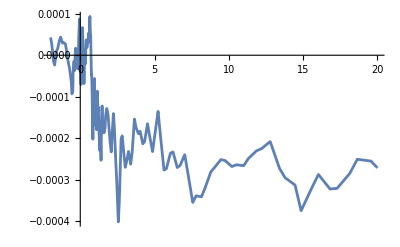

-Graphics-

{150,245,3}

./smicrow460_wavelengths.csv

./smicrow460_wavelengths_2.csv

./smicrow460_wavelengths_3.csv

```mathematica
interpolation2 = smicrow4602int;
dataset = smicrow4602;
smicrow460int22[t_,w_]:=Module[{},result = interpolation2[t,w]-Mean[interpolation2[#,w]&/@Table[i,{i,100,-2000,-100}]]];
tims=DeleteDuplicates[dataset[[;;,1]]];
wavs=DeleteDuplicates[dataset[[;;,2]]];

map=Table[{t,nm,smicrow460int22[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./smicrow460_map_replicate_2.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]]

interpolation3 = smicrow4603int;
dataset = smicrow4603;
smicrow460int23[t_,w_]:=Module[{},result = interpolation3[t,w]-Mean[interpolation3[#,w]&/@Table[i,{i,100,-2000,-100}]]];
tims=DeleteDuplicates[dataset[[;;,1]]];
wavs=DeleteDuplicates[dataset[[;;,2]]];
map=Table[{t,nm,smicrow460int23[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./smicrow460_map_replicate_3.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]]
```

```mathematica
(* -------------------- mScarlet500int2 ------------------------ *)

mScarlet500int2[t_,w_]:=Module[{},result = mScarlet500int[t,w]-Mean[mScarlet500int[#,w]&/@Table[i,{i,0,-2000,-50}]]];

plot2=DensityPlot[1000*mScarlet500int2[t*1000,w],{w,550,680},{t,-2,5},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

Plot[{1000*Mean[Table[mScarlet500int2[t,w],{t,0,100,750}]]},{w,600,680},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

Plot[{Mean[Table[mScarlet500int2[t+200,w],{w,590,610,1}]],Mean[Table[mScarlet500int2[t+200,w],{w,620,640,1}]]},{t,-500,3000},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Time [ps]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[mScarlet500[[;;,1]]];
wavs=DeleteDuplicates[mScarlet500[[;;,2]]];
map=Table[{t,nm,mScarlet500int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./mScarlet500_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./mScarlet500_wavelengths.csv",Table[{w,1000*Mean[Table[mScarlet500int2[t,w],{t,100,1000,200}]]},{w,wavs}]]
Export["./mScarlet500_transient.csv",Table[{t,Mean[Table[mScarlet500int2[t+200,w],{w,590,610,1}]],Mean[Table[mScarlet500int2[t+200,w],{w,620,640,1}]]},{t,tims}]]
```

-Graphics-

-Graphics-

-Graphics-

{118,245,3}

./mScarlet500_wavelengths.csv

InterpolatingFunction::dmval: Input value {192432.,590} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {192432.,591} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {192432.,592} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

./mScarlet500_transient.csv

```mathematica
(* -------------------- rhodo500int ------------------------ *)

rhodo500int2[t_,w_]:=Module[{},result = rhodo500int[t,w]-Mean[rhodo500int[#,w]&/@Table[i,{i,0,-2000,-100}]]];
plot2=DensityPlot[1000*rhodo500int2[t*1000,w],{w,520,800},{t,-2,10},PlotRange->All,PlotPoints->200,ColorFunction->"RedBlueTones",ImageSize->360,FrameLabel->{{"Time [ps]"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
Plot[{1000*Mean[Table[rhodo500int2[t,w],{t,50,2000,100}]]},{w,520,800},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]

tims=DeleteDuplicates[rhodo500[[;;,1]]];
wavs=DeleteDuplicates[rhodo500[[;;,2]]];
map=Table[{t,nm,rhodo500int2[t,nm]},{t,tims},{nm,wavs}];
Dimensions[map]
Export["./rhodo500_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
Export["./rhodo500_wavelengths.csv",Table[{w,1000*Mean[Table[rhodo500int2[t,w],{t,100,1000,200}]]},{w,wavs}]]
```

-Graphics-

-Graphics-

{118,245,3}

./rhodo500_wavelengths.csv

{118,245,3}

```mathematica
Plot[{1000*Mean[Table[sync7942w460int2[t,w],{t,100,10000,200}]],1000*Mean[Table[arabidopsisw460int2[t,w],{t,100,10000,200}]],1000*Mean[Table[chlamyw460int2[t,w],{t,100,10000,200}]],1000*Mean[Table[phaeow460singleint2[t,w],{t,100,10000,200}]],
1000*Mean[Table[smicrow460int23[t,w],{t,100,10000,200}]],1000*Mean[Table[mScarlet500int2[t,w],{t,100,10000,200}]],1000*Mean[Table[rhodo500int2[t,w],{t,100,10000,200}]]},{w,520,800},PlotRange->All,PlotPoints->200,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Wavelength [nm]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black}]
```

```mathematica
Export["sync7942w460int2_spectra.csv",Table[{w,1000*Mean[Table[sync7942w460int2[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["arabidopsisw460int2_spectra.csv",Table[{w,1000*Mean[Table[arabidopsisw460int2[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["chlamyw460int2_spectra.csv",Table[{w,1000*Mean[Table[chlamyw460int2[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["phaeow460singleint2_spectra.csv",Table[{w,1000*Mean[Table[phaeow460singleint2[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["smicrow460int23_spectra.csv",Table[{w,1000*Mean[Table[smicrow460int23[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["mScarlet500int2_spectra.csv",Table[{w,1000*Mean[Table[mScarlet500int2[t,w],{t,100,10000,200}]]},{w,520,800}]]
Export["rhodo500int2_spectra.csv",Table[{w,1000*Mean[Table[rhodo500int2[t,w],{t,100,10000,200}]]},{w,520,800}]]
```

sync7942w460int2_spectra.csv

arabidopsisw460int2_spectra.csv

chlamyw460int2_spectra.csv

phaeow460singleint2_spectra.csv

smicrow460int23_spectra.csv

mScarlet500int2_spectra.csv

rhodo500int2_spectra.csv

```mathematica
Plot[{1000*Mean[Table[sync7942w460int2[t,w],{w,710,750,1}]],1000*Mean[Table[arabidopsisw460int2[t,w],{w,710,750,1}]],1000*Mean[Table[chlamyw460int2[t,w],{w,710,750,1}]],1000*Mean[Table[phaeow460singleint2[t,w],{w,710,750,1}]],
1000*Mean[Table[smicrow460int23[t,w],{w,710,750,1}]],1000*Mean[Table[mScarlet500int2[t,w],{w,710,750,1}]],1000*Mean[Table[rhodo500int2[t,w],{w,710,750,1}]]},{t,100,10000},PlotRange->All,ImageSize->360,Frame->True,FrameLabel->{{"mdOD"," "},{"Time [fs]"," "}},LabelStyle->{FontSize-> 13,FontFamily->"Helvetica",Black},PlotLegends->Automatic]
```

```mathematica
Export["sync7942w460int2_wavelength.csv",Table[{w,1000*Mean[Table[sync7942w460int2[t,w],{w,710,750,1}]]},{t,times}]]
Export["arabidopsisw460int2_wavelength.csv",Table[{w,1000*Mean[Table[arabidopsisw460int2[t,w],{w,710,750,1}]]},{t,times}]]
Export["chlamyw460int2_wavelength.csv",Table[{w,1000*Mean[Table[chlamyw460int2[t,w],{w,710,750,1}]]},{t,times}]]
Export["phaeow460singleint2_wavelength.csv",Table[{w,1000*Mean[Table[phaeow460singleint2[t,w],{w,710,750,1}]]},{t,times}]]
Export["smicrow460int23_wavelength.csv",Table[{w,1000*Mean[Table[smicrow460int23[t,w],{w,710,750,1}]]},{t,times}]]
Export["mScarlet500int2_wavelength.csv",Table[{w,1000*Mean[Table[mScarlet500int2[t,w],{w,710,750,1}]]},{t,times}]]
Export["rhodo500int2_wavelength.csv",Table[{w,1000*Mean[Table[rhodo500int2[t,w],{w,710,750,1}]]},{t,times}]]
```